# Playing with the hydrogen atom (and spherical harmonics)

Yorick Reum, 2020
for “Hauptseminar Theoretische Physik”
Prof. Dr. Sara Buson, Prof. Dr. Ewelina Hankiewicz
Julius-Maximilians-Universität Würzburg

## Basic SphericalPlot3D for real part of spherical harmonics

```mathematica
Table[
SphericalPlot3D[
Re[SphericalHarmonicY[4,m,θ,ϕ]],
{θ,0,Pi},
{ϕ,0,2 Pi}
],
{m,0,4}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Use a self defined color grading to also show the phase / imaginary part

```mathematica
plotSpherical[l_, m_] := Module[
{Y, graphicsRow},
Y[θ_,ϕ_] := SphericalHarmonicY[l,m,θ,ϕ];
Hue2Pi[h_] := Hue[h/(2π)];
colFun[x_,y_,z_,θ_,ϕ_,r_] :=Hue2Pi[Arg[Y[θ,ϕ]]];
axesLabel = {Text[Style["x",Bold,12]],Text[Style["y",Bold,12]],Text[Style["z",Bold,12]]};
graphicsRow = GraphicsRow[{
SphericalPlot3D[
Abs[Y[θ,ϕ]],
{θ,0,π},
{ϕ,0,2π},
ColorFunction->colFun,
ColorFunctionScaling->False,
AxesLabel->axesLabel,
LabelStyle->Directive[White],
PerformanceGoal->"Quality",
Axes->True,
AxesStyle->Directive[White,Thickness[.004]],
BoxStyle->Directive[White,Thickness[.001]],
TicksStyle->Directive[White],
SphericalRegion->True,
PlotRange->All,
ViewPoint->{Front,Top,Left},
MeshStyle->Directive[LightGray]
(*ImageSize->Full *) 
],
BarLegend[
{Function[h,Hue2Pi[h]], {0,2π+0.01}},
Ticks->{0,{π/2,"π/2"},{π,"π"}, {3/2 π,"3/2π"},{2π,"2π"}},
LegendMargins-> 0,
LabelStyle->Directive[White]
]
},
ImagePadding->10
]
]
```

Plot the absolute value of the spherical harmonics together with there phase color graded for l = 3, m = 1:

```mathematica
plotSpherical[3, 1]
```

-Graphics-

Use Manipulate[] to simply select different l and m:

```mathematica
Manipulate[
If[m>l,m=l];
If[m<-l,m=-l];
plotSpherical[l,m]
(*ColorNegate[plotSpherical[l,m]]*),
{{l,0,Style["l",Italic]},0,4,1},
{{m,0,Style["m",Italic]},Range[-l,l]},
TrackedSymbols:>{l,m},ControlType->SetterBar,SaveDefinitions->True
]
```

## But what does spherical plot actually plot? (ϕ, θ, f)

```mathematica
r[x_,y_,z_] := √(x^2+y^2+z^2)
θ[x_,y_,z_] := ArcCos[z/r[x,y,z]]
ϕ[x_,y_,z_] := Piecewise[{{ArcTan[y/x], x >0}, {Sign[y] π/2, x == 0}, {ArcTan[y/x]+π, (x<0) ∧ (y ≥ 0)}, {ArcTan[y/x]-π, (x<0) ∧ (y < 0)}}]
```

```mathematica
x[r_,θ_,ϕ_]:=r Sin[θ]Cos[ϕ]
y[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ]
z[r_,θ_,ϕ_]:=r Cos[θ]
```

Demonstrate the functionality of spherical plot by using ContourPlot:
(Warning: intensive numerics used, will annoy your CPU.)

```mathematica
Y[θ_,ϕ_] := SphericalHarmonicY[l,m,θ,ϕ] /. {l-> 1, m-> 1};
size = 1;
ContourPlot3D[
  r[x,y,z] ==  Abs[Y[θ[x,y,z],ϕ[x,y,z]]]/size ,
{x,-size,size},
{y,-size,size},
{z,-size,size},
PlotPoints->20,
BoxRatios->Automatic,
ColorFunction->Function[{x,y,z},Hue2Pi[Arg[Y[θ[x,y,z],ϕ[x,y,z]]]]],
ColorFunctionScaling->False,
AxesLabel->axesLabel,
LabelStyle->Directive[Black],
PerformanceGoal->"Speed",
Mesh->None,
Axes->True,
AxesStyle->Directive[Black,Thickness[.004]],
BoxStyle->Directive[Black,Thickness[.001]],
TicksStyle->Directive[Black],
PlotRange->All,
ViewPoint->{Front,Top,Left},
MeshStyle->Directive[LightGray]
(*ImageSize->Full *) 
]
```

-Graphics3D-

Compare to SphericalPlot3D:

```mathematica
SphericalPlot3D[
Abs[Y[θ,ϕ]],
{θ,0,π},
{ϕ,0,2π},
ColorFunction->colFun,
ColorFunctionScaling->False,
AxesLabel->axesLabel,
LabelStyle->Directive[Black],
PerformanceGoal->"Quality",
Axes->True,
AxesStyle->Directive[Black,Thickness[.004]],
BoxStyle->Directive[Black,Thickness[.001]],
TicksStyle->Directive[Black],
SphericalRegion->True,
PlotRange->All,
ViewPoint->{Front,Top,Left},
MeshStyle->Directive[LightGray]
(*ImageSize->Full *) 
]
```

-Graphics3D-

## For the fun of it: Find a spherical function looking like Corona virus …

```mathematica
Manipulate[SphericalPlot3D[1+Sin[15 ϕ] Sin[13 θ]/pointiness,{θ,0,π},{ϕ,0,2 π},ColorFunction->(ColorData["DarkRainbow"][#6]&),Mesh->None,PlotPoints->35,Boxed->False,Axes->False,PlotRange->All],{pointiness,0.1,5}]
```

## … and try to approximate it by polynomials and spherical harmonics:

```mathematica
Corona[θ_, ϕ_] := 2+ Sin[4θ]* Sin[3ϕ] (* -1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ] *)
```

```mathematica
taylorCorona = Normal[Series[Corona[θ, ϕ],{θ,0,5},{ϕ,0,5}]]
```

2+θ^3 (-32 ϕ+48 ϕ^3-(108 ϕ^5)/5)+θ (12 ϕ-18 ϕ^3+(81 ϕ^5)/10)+θ^5 ((128 ϕ)/5-(192 ϕ^3)/5+(432 ϕ^5)/25)

```mathematica
sphplotCorona = SphericalPlot3D[
Corona[θ,ϕ],
{θ,0,π},{ϕ,0,2 π},
ColorFunction->(ColorData["DarkRainbow"][#6]&),
Mesh->None,
PlotPoints->35,
Boxed->True,
Axes->True,
PlotRange->All
]
```

-Graphics3D-

Expansion coefficients for spherical harmonics:

```mathematica
a[l_,m_, f_] := Module[
{int,θ,ϕ},
Assuming[
{θ ∈ Reals, ϕ ∈Reals},
int = Integrate[
Integrate[
Conjugate[SphericalHarmonicY[l,m,θ,ϕ]] * f[θ,ϕ]*Sin[θ],
θ
],
ϕ
];
int = (int /. θ -> π) - (int /. θ -> 0);
int = (int /. ϕ -> 2π) - (int /. ϕ -> 0)
]
]
```

or simply:

```mathematica
a[l_,m_, f_] := Integrate[
Conjugate[SphericalHarmonicY[l,m,θ,ϕ]] * f[θ,ϕ]*Sin[θ],
{ϕ,0,2π},{θ,0,π}
]
```

```mathematica
CoronaDevExample[θ_, ϕ_] := Sum[
Sum[
a[l,m, Corona] * Subscript[Y,l,m][θ, ϕ],
{m,-l,l}
],
{l,0,1}
]
```

How does any expansion like this look like?

```mathematica
CoronaDevExample[θ, ϕ]
```

4 √π Y_(0,0)[θ,ϕ]

… and now with actual SphericalHarmonicY[] not just a function called Y:

```mathematica
CoronaDev[θ_, ϕ_,lmax_] := Sum[
Sum[
a[l,m, Corona] * SphericalHarmonicY[l,m,θ,ϕ],
{m,-l,l}
],
{l,0,lmax}
]
```

Calculate them for l up to 10:

```mathematica
cdTabIndexed = Table[
cd = CoronaDev[θ, ϕ,lmax];
Labeled[
SphericalPlot3D[
cd,
{θ,0,π},{ϕ,0,2 π},
ColorFunction->(ColorData["DarkRainbow"][#6]&),
Mesh->None,
PlotPoints->35,
Boxed->False,
Axes->False,
PlotRange->All
],
Style["l ≤ " <> ToString[lmax], White, Larger, Bold]
],
{lmax,0,10}
]
```

{-Graphics3D-l ≤ 0,-Graphics3D-l ≤ 1,-Graphics3D-l ≤ 2,-Graphics3D-l ≤ 3,-Graphics3D-l ≤ 4,-Graphics3D-l ≤ 5,-Graphics3D-l ≤ 6,-Graphics3D-l ≤ 7,-Graphics3D-l ≤ 8,-Graphics3D-l ≤ 9,-Graphics3D-l ≤ 10}

Export this expansion as a .gif animation (because we can):

```mathematica
Export["/your/favorite/path/sphericalApproxAnimate.gif",cdTabIndexed, Background-> RGBColor["#003462"], "DisplayDurations" -> .5]
```

## Let us create a table of spherical harmonic plots:

```mathematica
plotSphericalTab[l_, m_] := Module[
{Y, graphicsRow},
Y[θ_,ϕ_] := SphericalHarmonicY[l,m,θ,ϕ];
Hue2Pi[h_] := Hue[h/(2π)];
colFun[x_,y_,z_,θ_,ϕ_,r_] :=Hue2Pi[Arg[Y[θ,ϕ]]];
axesLabel = {Text[Style["x",Bold,12]],Text[Style["y",Bold,12]],Text[Style["z",Bold,12]]};
plot = SphericalPlot3D[
Abs[Y[θ,ϕ]],
{θ,0,π},
{ϕ,0,2π},
ColorFunction->colFun,
ColorFunctionScaling->False,
AxesLabel->axesLabel,
LabelStyle->Directive[Black],
PerformanceGoal->"Quality",
Axes->False,
Boxed->False,
BoxStyle->None,
SphericalRegion->True,
PlotRange->All,
ViewPoint->{Front,Top,Left},
MeshStyle->None
(*ImageSize->Full*)
]
]
```

```mathematica
table = Table[Table[plotSphericalTab[l,m], {m,-l,l}],{l,0,4}];
```

```mathematica
tableForm = Style[
TableForm[
CenterArray[#,9, ""]& /@ table, 
TableHeadings->{Table["l = "<>ToString[l],{l,0,4}],Table["m = "<>ToString[m],{m,-4,4}]},
TableAlignments->Center
],
 Directive[White,Thickness[.004]],
FontSize->32,
FontFamily->"CMU Classical Serif" (* classic LaTeX font *)
]
```

| m = -4 | m = -3 | m = -2 | m = -1 | m = 0 | m = 1 | m = 2 | m = 3 | m = 4
l = 0 |  |  |  |  | -Graphics3D- |  |  |  | 
l = 1 |  |  |  | -Graphics3D- | -Graphics3D- | -Graphics3D- |  |  | 
l = 2 |  |  | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |  | 
l = 3 |  | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | 
l = 4 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

## Plot the radial part of the wave function:

```mathematica
Laguerre[m_,x_] := Exp[x] D[x^m Exp[-x],{x,m}]
LaguerreLAss[m_,p_,x_] := D[Laguerre[m,ξ],{ξ,p}] /. ξ -> x
Nsq[n_,l_] := ((2 Z)/n)^3((n-l-1)!)/(2n ((n+l)!)^3) /. Z -> 1
R[n_,l_,ρ_] := -√Nsq[n,l] Exp[(- Z)/n ρ] ((2 Z ρ)/n)^l LaguerreLAss[n+l,(2l+1),((2 Z ρ)/n)] /. Z -> 1
```

Let us plot some examples of the probability density:

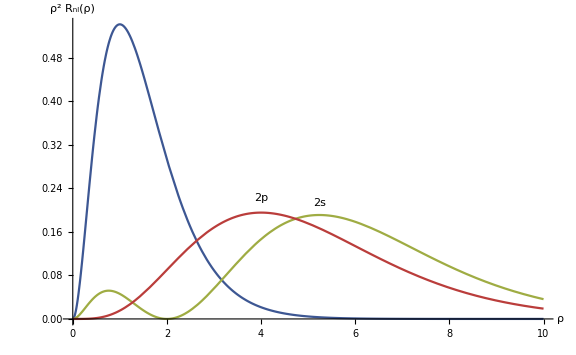

```mathematica
funcs = {ρ^2 R[1,0,ρ]^2,
ρ^2 R[2,0,ρ]^2,
ρ^2 R[2,1,ρ]^2
};
maxima = Flatten@((ρ /.#)&/@ Solve[D[#,ρ] == 0 ∧ ρ > 0 ∧ D[#,{ρ,2}] < 0,ρ]& /@ funcs);
radialPlot = Plot[
funcs,
{ρ,0,10},
ImageSize->Large,
AxesLabel->{"ρ","ρ^2 R_nl(ρ)"},
PlotLabels->Placed[{"1s","2s","2p"},Above],
LabelStyle->Directive[Background-> None],
LabelStyle->Directive[White,Larger],
Ticks->{Table[i,{i,0,10}],Automatic},
PlotStyle->"DarkRainbow",
AxesStyle->Directive[White],
TicksStyle->Directive[White],
Axes->True,
GridLines->{maxima, None},
GridLinesStyle->Directive[Dotted, White]
]
```

## And now the wave function itself (absolutes only):

```mathematica
ψ[n_,l_,m_,ρ_,θ_,ϕ_]:=R[n,l,ρ] SphericalHarmonicY[l,m,θ,ϕ]
```

Plot the probability density (reduced to 2D using symmetries):

```mathematica
func = (√(x^2+y^2))ψ[1,0,0,√(x^2+y^2),ArcCos[x/(√(x^2+y^2))],ϕ];
sq = 5;
Hue2Pi[h_] := Hue[h/(2π)];
colFun[ξ_,γ_] :=Hue2Pi[Arg[func /. {x-> ξ, y -> γ}]]
ticks = Table[i,{i,-5,5}];
ticksZ = Table[i,{i,0,0.05,0.01}];
func // FullSimplify
plot3D100Density = Plot3D[
 Abs[func]^2,
{x,-sq,sq},
{y,-sq,sq},
PlotRange->{{-sq,sq},{-sq,sq},{0,0.05}},
(* ColorFunction->"DarkRainbow", *)
ColorFunction-> colFun,
PerformanceGoal->"Quality",
PlotPoints->500,
ImageSize->Large,
Ticks->{ticks,ticks,Automatic},
FaceGrids->{{{0,1,0},{ticks,ticksZ}},{{-1,0,0},{ticks,ticksZ}}},
Mesh->Automatic,
MeshStyle->Directive[Orange],
AxesStyle->Directive[White, 14],
AxesLabel->{"x","y"},
PlotLabel->Style["|ρ ψ_(1, 0, 0)(x,y)|^2",White,FontSize->24,"Graphics"]
]
```

(ⅇ^(-√(x^2+y^2)) √(x^2+y^2))/(√π)

-Graphics3D-

And the actual wavefunction:

```mathematica
func = ψ[1,0,0,√(x^2+y^2),ArcCos[x/(√(x^2+y^2))],ϕ];
sq = 5;
Hue2Pi[h_] := Hue[h/(2π)];
colFun[ξ_,γ_] :=Hue2Pi[Arg[func /. {x-> ξ, y -> γ}]]
ticks = Table[i,{i,-5,5}];
ticksZ = Table[i,{i,0,0.5,0.1}];
func // FullSimplify
plot3D100Density = Plot3D[
 func,
{x,-sq,sq},
{y,-sq,sq},
PlotRange->{{-sq,sq},{-sq,sq}, Full},
(* ColorFunction->"DarkRainbow", *)
ColorFunction-> colFun,
PerformanceGoal->"Quality",
ImageSize->Large,
Ticks->{ticks,ticks,Automatic},
FaceGrids->{{{0,1,0},{ticks,ticksZ}},{{-1,0,0},{ticks,ticksZ}}},
Mesh->Automatic,
MeshStyle->Directive[Orange],
AxesStyle->Directive[White, 14],
AxesLabel->{"x","y"},
PlotLabel->Style["ψ_(1, 0, 0)(x,y)",White,FontSize->24,"Graphics"]
]
```

(ⅇ^(-√(x^2+y^2)))/(√π)

-Graphics3D-

```mathematica
func = (√(x^2+y^2))ψ[2,1,0,√(x^2+y^2),ArcCos[x/(√(x^2+y^2))],ϕ];
sq = 15;
Hue2Pi[h_] := Hue[h/(2π)];
colFun[ξ_,γ_] :=Hue2Pi[Arg[func /. {x-> ξ, y -> γ}]]
ticks = Table[i,{i,-5,5}];
ticksZ = Table[i,{i,0,0.05,0.01}];
func // FullSimplify
plot3D100Density = Plot3D[
 Abs[func]^2,
{x,-sq,sq},
{y,-sq,sq},
PlotRange->{{-sq,sq},{-sq,sq},{0,0.05}},
(* ColorFunction->"DarkRainbow", *)
ColorFunction-> colFun,
PerformanceGoal->"Quality",
ImageSize->Large,
Ticks->{ticks,ticks,Automatic},
FaceGrids->{{{0,1,0},{ticks,ticksZ}},{{-1,0,0},{ticks,ticksZ}}},
Mesh->Automatic,
MeshStyle->Directive[Orange],
AxesStyle->Directive[White, 14],
AxesLabel->{"x","y"},
PlotLabel->Style["|ρ ψ_(2, 1, 0)(x,y)|^2",White,FontSize->24,"Graphics"]
]
```

(ⅇ^(-1/2 √(x^2+y^2)) x √(x^2+y^2))/(4 √(2 π))

-Graphics3D-

## And now the wave function itself including its phase:

Quick example for the probability density using color grading for the phase:

```mathematica
Y[θ_,ϕ_] := SphericalHarmonicY[0,0,θ,ϕ];
Hue2Pi[h_] := Hue[h/(2π)];
colFun[x_,y_,z_,θ_,ϕ_,r_] :=Hue2Pi[Arg[Y[θ,ϕ]]];
axesLabel = {Text[Style["x",Bold,12]],Text[Style["y",Bold,12]],Text[Style["z",Bold,12]]};
graphicsRow = GraphicsRow[{
SphericalPlot3D[
r^2 Abs[ψ[1,0,0,r,θ,ϕ]]^2 /. r -> 1,
{θ,0,π},
{ϕ,0,2π},
ColorFunction->colFun,
ColorFunctionScaling->False,
AxesLabel->axesLabel,
LabelStyle->Directive[Black],
PerformanceGoal->"Quality",
Axes->True,
AxesStyle->Directive[White,Thickness[.004]],
BoxStyle->Directive[White,Thickness[.001]],
TicksStyle->Directive[White],
SphericalRegion->True,
PlotRange->All,
ViewPoint->{Front,Top,Left},
MeshStyle->Directive[LightGray]
(*ImageSize->Full *) 
],
BarLegend[
{Function[h,Hue2Pi[h]], {0,2π+0.01}},
Ticks->{0,{π/2,"π/2"},{π,"π"}, {3/2 π,"3/2π"},{2π,"2π"}},
LegendMargins-> 0,
LabelStyle->Directive[White]
]
},
ImagePadding->10
]
```

-Graphics-

## Finding a better representation for the wave function – plotting the probability density as a actual density

```mathematica
plotOrbitalDensity[sq_,n_,l_,m_] := Module[
{x,y,z},
f=TransformedField["Spherical"->"Cartesian",ψ[n,l,m,ρ,θ,ϕ],{ρ,θ,ϕ}->{x,y,z}];
DensityPlot3D[
 (√(x^2+y^2+z^2))^2 Abs[f]^2,
{x,-sq,sq},
{y,-sq,sq},
{z,-sq,sq},
RegionFunction->Function[{x,y,z},x<0||y>0],
ColorFunction->Hue,
PlotLegends->Placed[Automatic,Left],
ColorFunctionScaling->True,
AxesLabel->{"x [a_0]","y [a_0]","z [a_0]"},
ViewPoint->{1.3,-2.4,1.},
PerformanceGoal->"Quality",
FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},
LabelStyle->Directive[White,16],
AxesStyle->Directive[White,14],
ImageSize->Medium,
Ticks->Table[
Table[
{j,ToString[j]},
{j,-sq,sq,sq/3}
],{i,3}]
]
]
```

Example plot for n = 2, m = 0, l = 0, plot region from - 15 a_0 to + 15 a_0.
Color grading is probability density now.

```mathematica
plotOrbitalDensity[15,2,0,0]
```

-Graphics3D-